Solución: Definimos la función y la graficamos

Piecewise[{{Abs[t-3]-4, Abs[t-3]<4}, {0, True}}]

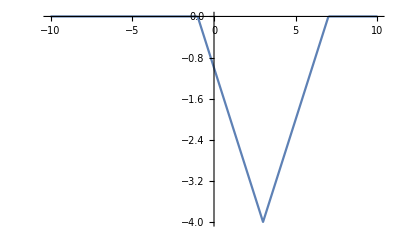

```mathematica
Clear[f,t,x,e]
TraditionalForm[Piecewise[{{Abs[t-3]-4,Abs[t-3]<4},{0,Abs[t-3]>4}}]]
Plot[Piecewise[{{Abs[t-3]-4,Abs[t-3]<4},{0,Abs[t-3]>4}}],{t,-10,10}]
```

Reescribimos la función de una manera más sencilla para realizar la integral de la transformada de Fourier:

Piecewise[{{0, -∞<t<-1}, {-t-1, -1<t<3}, {t-7, 3<t<7}}]

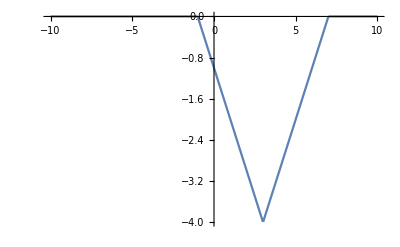

```mathematica
f[t_]=Piecewise[{{0,-∞<t<-1},{-t-1,-1<t<3},{t-7,3<t<7},{0,7<t<∞}}];
TraditionalForm[f[t]]
Plot[f[t],{t,-10,10}]
```

Ahora se usa la integral de la transformada de Fourier para cada dominio:

∫_(-∞)^∞ f[t]*e^(-2*π*ⅈ*w*t)ⅆt=∫_(-∞)^-1 f[t]*e^(-2*π*ⅈ*w*t)ⅆt+∫_-1^3 f[t]*e^(-2*π*ⅈ*w*t)ⅆt+∫_3^7 f[t]*e^(-2*π*ⅈ*w*t)ⅆt+

```mathematica
∫_(-∞)^-1 f[t]*E^(-2*π*ⅈ*w*t)ⅆt
```

0

```mathematica
∫_-1^3 f[t]*E^(-2*π*ⅈ*w*t)ⅆt
```

(ⅇ^(-6 ⅈ π w) (-1+ⅇ^(8 ⅈ π w)-8 ⅈ π w))/(4 π^2 w^2)

```mathematica
∫_3^7 f[t]*E^(-2*π*ⅈ*w*t)ⅆt
```

(ⅇ^(-14 ⅈ π w) (1-ⅇ^(8 ⅈ π w)+8 ⅈ ⅇ^(8 ⅈ π w) π w))/(4 π^2 w^2)

```mathematica
∫_7^∞ f[t]*E^(-2*π*ⅈ*w*t)ⅆt
```

0

Ahora sumamos los resultados:

```mathematica
∫_(-∞)^-1 f[t]*E^(-2*π*ⅈ*w*t)ⅆt+∫_-1^3 f[t]*E^(-2*π*ⅈ*w*t)ⅆt+∫_3^7 f[t]*E^(-2*π*ⅈ*w*t)ⅆt+∫_7^∞ f[t]*E^(-2*π*ⅈ*w*t)ⅆt
```

(ⅇ^(-6 ⅈ π w) (-1+ⅇ^(8 ⅈ π w)-8 ⅈ π w))/(4 π^2 w^2)+(ⅇ^(-14 ⅈ π w) (1-ⅇ^(8 ⅈ π w)+8 ⅈ ⅇ^(8 ⅈ π w) π w))/(4 π^2 w^2)

Y simplificamos:

```mathematica
ExpToTrig[FullSimplify[(ⅇ^(-6 ⅈ π w) (-1+ⅇ^(8 ⅈ π w)-8 ⅈ π w))/(4 π^2 w^2)+(ⅇ^(-14 ⅈ π w) (1-ⅇ^(8 ⅈ π w)+8 ⅈ ⅇ^(8 ⅈ π w) π w))/(4 π^2 w^2)]]
```

-(Cos[6 π w] Sin[4 π w]^2)/(π^2 w^2)+(ⅈ Sin[4 π w]^2 Sin[6 π w])/(π^2 w^2)

Además comprobamos que el resultado es correcto:

```mathematica
F[w_]=ExpToTrig[FullSimplify[∫_(-∞)^∞ f[t]*E^(-2*π*ⅈ*w*t)ⅆt]]
```

-(Cos[6 π w] Sin[4 π w]^2)/(π^2 w^2)+(ⅈ Sin[4 π w]^2 Sin[6 π w])/(π^2 w^2)

Podemos apreciar que la parte real es: 

Re[F[f(t)](ω)]=-(Cos[6 π ω] Sin[4 π ω]^2)/(π^2 ω^2)

Y la transformada evaluada en ω=π/3

```mathematica
Simplify[F[π/3]]
```

-(9 Sin[(4 π^2)/3]^2 (Cos[2 π^2]-ⅈ Sin[2 π^2]))/π^4